Should work now with timelike or null curves (ur(0) is found by normalising the velocity and can be set uu=0 if you want, the geodesic equation should be the same either way) but need to set up particles in a way that would look good to demonstrate the null paths, let’s see.
This is working for null paths! Need to add a manipulate section to get a handle on the range of good initial conditions but it’s working!
Want to set up a wall of parallel incoming rays to see what happens as each one approaches the black hole. Let’s get one up and running first.

```mathematica
(*Initial Conditions*)
(*L0 = 72/(√395);
E0 = √(217/237);*)
(*L0 = 3.72737;*)
E0 = 0.6;

x0=15;
y0=10;
ux0=-1;
uy0=0;

r0 = √(x0^2+y0^2);
ϕ0 = ArcTan[y0/x0];
ur0=(x0 ux0 + y0 uy0)/r0;
uϕ0=(x0 uy0 -y0 ux0)/r0^2;

t0=0;
θ0=π/2;
M0 = 1;
NullOrTimelike = 0;
```

```mathematica
(* Set the dimension and coordinate system *)
d = 4;
coords={t, r, θ, ϕ};
```

```mathematica
(* Define the metric (Schwarzschild here) *)
f[r_]:=1-(2M)/r;
metric={{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
inverseMetric=Simplify[Inverse[metric]];
```

```mathematica
(* Define initial velocities for t and ϕ above, then find initial r-velocity from normalisation of the vector. Set null or timelike path above *)
(*u = {ut, ur, uθ, uϕ};*)
u[α_]:=D[coords[[α]][τ],τ];
metricOfτ=metric/.{t->t[τ],r->r[τ],θ->θ[τ],ϕ->ϕ[τ]};
guuEq = Sum[metricOfτ[[a,b]]u[a]u[b], {a, 1, d}, {b, 1, d}];
(*ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]*)
ut0=Simplify[SolveValues[guuEq==NullOrTimelike, t'[τ]]][[2]]/.{ r[τ]->r0, t[τ]->t0, θ[τ]->θ0, ϕ[τ]->ϕ0, r'[τ]->ur0, θ'[τ]->0, ϕ'[τ]->uϕ0}/.M->M0
```

(5 √(13 (9/13+(4 (-2+5 √13))/(65 √13))))/(-2+5 √13)

```mathematica
(* Calculate the Christoffel Symbol *)
Γ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ];
(* Ask Niels if this is a good way to go about it *)
(* Convert the general Christoffel connection to one where the coordinates are functions of time. Really I think this is swapping from the general connection to the connection between different paths or instances of the particle (i.e. we go from r as a coordinate to r_particle(τ) as a component of the position of this object) *)
(* I could also use the metric[τ] I used above but this is cleaner *)
ΓOfτ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ]/.{t->t[τ], r->r[τ], θ->θ[τ], ϕ->ϕ[τ]};
```

```mathematica
(* Get the geodesic equations for each component *)
timeEq=t''[τ]+Sum[ΓOfτ[[1,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
radialEq=r''[τ]+Sum[ΓOfτ[[2,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
θEq=θ''[τ]+Sum[ΓOfτ[[3,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
ϕEq=ϕ''[τ]+Sum[ΓOfτ[[4,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
```

```mathematica
(*EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==ur0, ϕ[0]==ϕ0, ϕ'[0]==uϕ0, t[0]==0, t'[0]==ut0, θ[0]==Pi/2, θ'[0]==0}*)
EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==ur0, ϕ[0]==ϕ0, ϕ'[0]==uϕ0, t[0]==0, t'[0]==ut0, θ[0]==Pi/2, θ'[0]==0}
```

{-(2 M r'[τ] t'[τ])/(2 M r[τ]-r[τ]^2)+t''[τ]==0,(M r'[τ]^2)/(2 M r[τ]-r[τ]^2)+(M (-2 M+r[τ]) t'[τ]^2)/r[τ]^3+(2 M-r[τ]) θ'[τ]^2+(2 M-r[τ]) Sin[θ[τ]]^2 ϕ'[τ]^2+r''[τ]==0,(2 r'[τ] θ'[τ])/r[τ]-Cos[θ[τ]] Sin[θ[τ]] ϕ'[τ]^2+θ''[τ]==0,(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ[τ]] θ'[τ] ϕ'[τ]+ϕ''[τ]==0,r[0]==5 √13,r'[0]==-3/(√13),ϕ[0]==ArcTan[2/3],ϕ'[0]==2/65,t[0]==0,t'[0]==(5 √(13 (9/13+(4 (-2+5 √13))/(65 √13))))/(-2+5 √13),θ[0]==π/2,θ'[0]==0}

```mathematica
solRange=40;
eomSol = Block[{M=M0, En=E0, L=L0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]]
```

{{r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

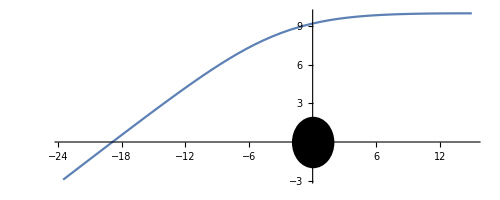

```mathematica
Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}],
Graphics[Disk[{0,0}, 2M0]]]
```

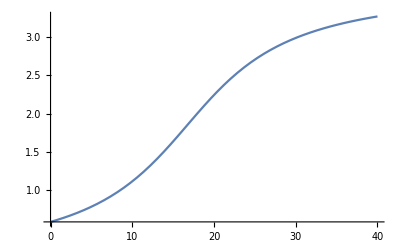

```mathematica
Show[Plot[Evaluate[{ϕ[τ]}/.eomSol],{τ,0,solRange}]]
```

```mathematica
Manipulate[
r0 = √(x0^2+y0^2);
ϕ0 = ArcTan[y0/x0];
ur0=(x0 ux0 + y0 uy0)/r0;
uϕ0=(x0 uy0 -y0 ux0)/r0^2;

ut0=Simplify[SolveValues[guuEq==NullOrTimelike, t'[τ]]][[2]]/.{ r[τ]->r0, t[τ]->t0, θ[τ]->θ0, ϕ[τ]->ϕ0, r'[τ]->ur0, θ'[τ]->0, ϕ'[τ]->uϕ0}/.M->M0;

EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==ur0, ϕ[0]==ϕ0, ϕ'[0]==uϕ0, t[0]==0, t'[0]==ut0, θ[0]==Pi/2, θ'[0]==0};

eomSol = Block[{M=M0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]];

Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}],
Graphics[Disk[{0,0}, 2M0]]], {{solRange, 5}, 5,40},{{y0,5},N[1, 10], 20}]
```

NDSolve::ndsz: At τ == 19.9902, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At τ == 28.5627, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At τ == 30.8824, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At τ == 34.0016, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At τ == 37.0898, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000816327,0,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000816327 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.